```mathematica
(* September 18, 2020 *)
(* Solving Friedmann eqn for 3 cases using NDSolve *)


(* Dr. McGuigan Case 1 (Dark energy, lambda, with curvature, k): k=1, lambda=3 (nonzero), rho=0 (m=0, C=0), c=1 *)
```

```mathematica
(* I'm using a simplified version of Friedmann eqn that I worked out on paper beforehand *)
(* Using NDSolve to solve the ODE with inital condition a'(t)=0.001 and plotting *)
```

```mathematica
ode1={a'[t]-(a[t]^(2)-1)^(1/2)==0,a'[0]==0.001};
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

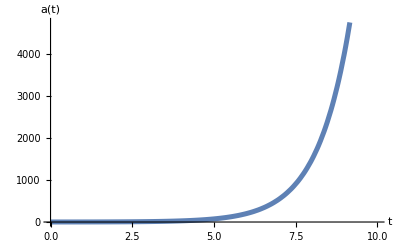

```mathematica
Plot[a[t]/.sol,{t,0,10},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotStyle->{Thickness[0.009]}]
```

```mathematica
(* Dr. McGuigan Case 2 (Dark energy, lambda, with matter, m): k=0, lambda=0.15, m=1 so rho=m/a^3, 8πG=c=1 *)
(* Using NDSolve to solve the ODE with inital condition a'(t)=0.0000001 and plotting *)

ode1={a'[t]-(((1/(3*a[t]))+0.05*(a[t]^2)))^(1/2)==0,a[0]==0.0000001};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

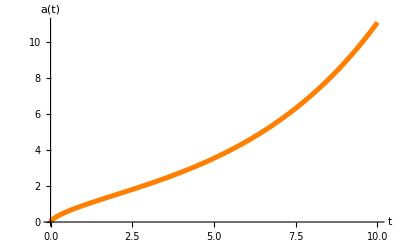

```mathematica
Plot[a[t]/.sol,{t,0,10},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotStyle->{Orange,Thickness[0.009]}]
```

```mathematica
(* Dr. McGuigan Case 3 (Dark energy, lambda, with radiation, C): k=0, rho=C/a^4 and C=1, lambda=0.15, 8πG=c=1 *)

ode1={a'[t]-((1/(3*a[t]^2))+(0.05*a[t]^2))^(1/2)==0,a[0]==0.0000001};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

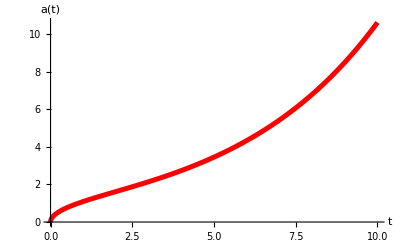

```mathematica
Plot[a[t]/.sol,{t,0,10},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotStyle->{Red,Thickness[0.009]}]
```

```mathematica
(* Case 4 (Einstein de Sitter i.e. matter, m, with flat space k, no cosmo constant): k=0, lambda=0, m=1 for rho=m/a^3, C=0, 8πG=c=1 *)
ode1={a'[t]-(1/(3*a[t]^2))^(1/2)==0,a[0]==0.001};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

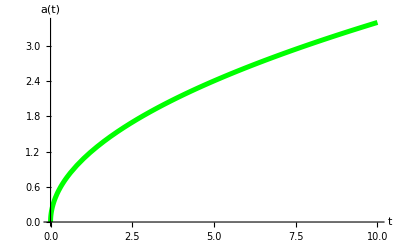

```mathematica
Plot[a[t]/.sol,{t,0,10},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotStyle->{Green,Thickness[0.009]}]
```